```mathematica
2+3
```

5

```mathematica
PDF[NormalDistribution[1,1],y]
```

(ⅇ^(-1/2 (-1+y)^2))/(√(2 π))

General::prng: The value of the option PlotRange -> {{Automatic,{0,1}},Automatic} is not All, Full, Automatic, a positive machine number or an appropriate list of range specifications.

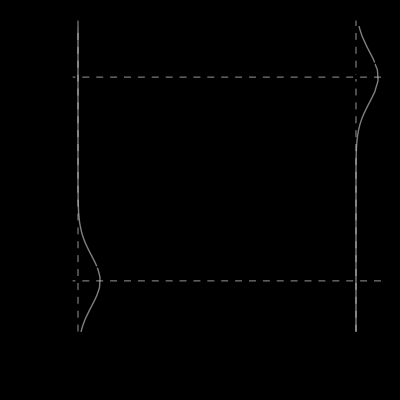

```mathematica
ContourPlot[{x==PDF[NormalDistribution[2,1],y],x-5==PDF[NormalDistribution[10,1],y]},{x,0,6},{y,0,12},PlotTheme->{"LargeLabels","Monochrome"},Background->Transparent,PlotRange->{{Automatic,{0,1}},Automatic},ContourStyle->Directive[Dashing[{}],Gray,Thick],FrameLabel->{x,y},FrameTicks->{{{{2,Subscript[μ, 2]},{10,Subscript[μ, 1]}},None}, {{0,{5,1}},None}},GridLines->{{0,5}, {2,10}},GridLinesStyle->Directive[Thin,Dashed],  Epilog->{Thick,PointSize[Large],InfiniteLine[{{0,2},{5,10}}],Point[{{0,2},{5,10}}]}]
```